```mathematica
"code that I think i'll use:
FindRoot[0==x1out[t],{t,50}]
datalist={{1.0,0},{1.5,0},{2.0,0},{3.0,0}}
graph9=ListPlot[datalist,AxesLabel→{"a", "Root Value (x)"}]"
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
Quit[]
```

```mathematica
"Guy F Mongelli                                       ChE 273: Process Dynamics
Professor Chimowitz                                   Dec. 7th 2009

Take Home Component of the Final Exam

Problem Statment:
1. Devlop a numerical dynamic simulation model for a 20 stage absorber-
stripper column along the lines discussed in class and investigate its
dynamic behaviore for various values of αϵ[.75,2]. Assume the
equilibrium constant, k, to be approx. 2.5.  To do this, study the exit
gas concentration dynamics for both step and pulse disturbances (of
various magnitudes) to the gas inlet stream-starting from baseline steady state
concentrations equal to zero.  Use software of your choice for the 
simulations (ie Mathematica, MATLAB)

Mathematica was utilized in the analyses conducted.
http://reference.wolfram.com/mathematica/tutorial/DSolveIntroduction.html
The approach to solving this problem is to construct a differential equation that represents the mass balance
accross an individual stage of the distillation column.  Different from chE 250, where steady state was assumed,
this problem will need to be time-dependent.  The equations for all but the top and bottom trays will appear very 
simmilar and be of the form seen below (result of mass balance).  The problem will be solved for a particular alpha value and then resolved 
at different values, each generating a graph of its own.  Since we know k, the ratio between the liquid 
and vapor flow rates can be calculated.  The above process will be repeated for different variations in
    the perturbation of the incoming concentration"
```

PART I: Perturbations in the Bottoms Vapor Concentration

Step Solution

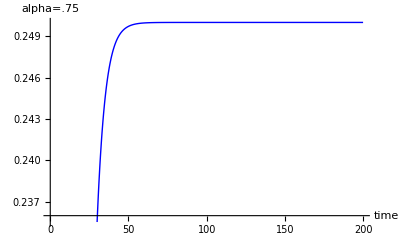

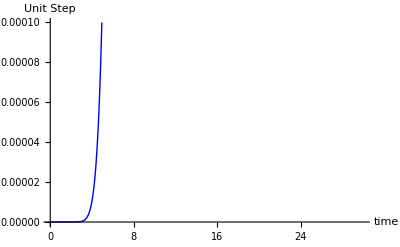

0.25

0.158

InterpolatingFunction::dmval: Input value {-460.`} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-78.53467280819373`} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-80.93966293878154`} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction will be suppressed during this calculation.

{t→19.0762}

10

{(0.25 ⅇ^(-10 s))/(s (1+s (t→19.0762)))}

{0.25 (1-ⅇ^(-(-10+t)/(t→19.0762))) HeavisideTheta[-10+t]}

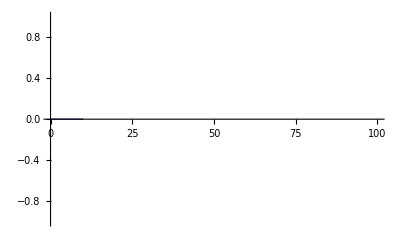

{0.25 (1-ⅇ^((10-t)/(t→19.0762)))}

-Graphics-

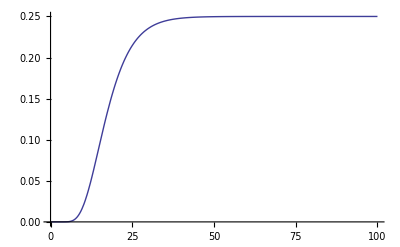

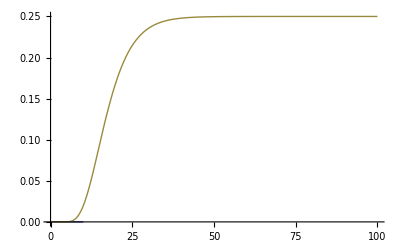

```mathematica
"PART I: Perturbations in the Bottoms Vapor Concentration"
"Step Solution"
a=2;
x0=0;
Xin=UnitStep[t];
Yin=Exp[-50*t^2];
diffsol=NDSolve[{x1'[t]==x0-(1+a)*x1[t]+a*x2[t],
x2'[t]==x1[t]-(1+a)*x2[t]+a*x3[t],
x3'[t]==x2[t]-(1+a)*x3[t]+a*x4[t],
x4'[t]==x3[t]-(1+a)*x4[t]+a*x5[t],
x5'[t]==x4[t]-(1+a)*x5[t]+a*x6[t],
x6'[t]==x5[t]-(1+a)*x6[t]+a*x7[t],
x7'[t]==x6[t]-(1+a)*x7[t]+a*x8[t],
x8'[t]==x7[t]-(1+a)*x8[t]+a*x9[t],
x9'[t]==x8[t]-(1+a)*x9[t]+a*x10[t],
x10'[t]==x9[t]-(1+a)*x10[t]+a*x11[t],
x11'[t]==x10[t]-(1+a)*x11[t]+a*x12[t],
x12'[t]==x11[t]-(1+a)*x12[t]+a*x13[t],
x13'[t]==x12[t]-(1+a)*x13[t]+a*x14[t],
x14'[t]==x13[t]-(1+a)*x14[t]+a*x15[t],
x15'[t]==x14[t]-(1+a)*x15[t]+a*x16[t],
x16'[t]==x15[t]-(1+a)*x16[t]+a*x17[t],
x17'[t]==x16[t]-(1+a)*x17[t]+a*x18[t],
x18'[t]==x17[t]-(1+a)*x18[t]+a*x19[t],
x19'[t]==x18[t]-(1+a)*x19[t]+a*x20[t],
x20'[t]==x19[t]-(1+a)*x20[t]+Xin,x1[0]==0,x2[0]==0,x3[0]==0,x4[0]==0,x5[0]==0,x6[0]==0,x7[0]==0,x8[0]==0,x9[0]==0,x10[0]==0,x11[0]==0,x12[0]==0,x13[0]==0,x14[0]==0,x15[0]==0,x16[0]==0,x17[0]==0,x18[0]==0,x19[0]==0,x20[0]==0},{x1[t],x2[t],x3[t],x4[t],x5[t],x6[t],x7[t],x8[t],x9[t],x10[t],x11[t],x12[t],x13[t],x14[t],x15[t],x16[t],x17[t],x18[t],x19[t],x20[t]},{t,0,200}];

{x1out[t_],x2out[t_],x3out[t_],x4out[t_],x5out[t_],x6out[t_],x7out[t_],x8out[t_],x9out[t_],x10out[t_],x11out[t_],x12out[t_],x13out[t_],x14out[t_],x15out[t_],x16out[t_],x17out[t_],x18out[t_],x19out[t_],x20out[t_]}={x1[t],x2[t],x3[t],x4[t],x5[t],x6[t],x7[t],x8[t],x9[t],x10[t],x11[t],x12[t],x13[t],x14[t],x15[t],x16[t],x17[t],x18[t],x19[t],x20[t]}/.Flatten[diffsol];
Plot[x1out[t],{t,0,200},AxesLabel->{"time","alpha=.75","Response to Unit Step Perturbation"},PlotStyle->{RGBColor[0,0,1]}]
Plot[x1out[t],{t,0,30},AxesLabel->{"time","Unit Step","Response to Unit Step Perturbation"},PlotStyle->{RGBColor[0,0,1]},PlotRange->{0,.0001}]

kp=(x1out[200]-x1out[0])
δ=.632*kp
τ=FindRoot[δ==x1out[t],{t,50}]
θ=10
G[s_]=(kp*Exp[-θ*s])/((τ*s+1)s)
S[t_]=InverseLaplaceTransform[G[s],s,t]
Plot[{S[t]},{t,0,100}]
f[t_]=kp(1-Exp[(θ-t)/τ])
Plot[{f[t]},{t,0,100}]
Plot[{x1out[t]},{t,0,100}]
Plot[{S[t],kp(1-Exp[(θ-t)/τ]),x1out[t]},{t,0,100}]
```

Step Solution

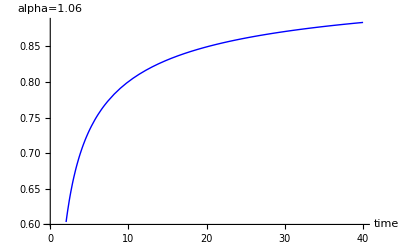

```mathematica
"Step Solution"
a=1.06;
x0=0;
Xin=UnitStep[t];
Yin=EXP[-50*t^2];
diffsol=NDSolve[{x1'[t]==x0-(1+a)*x1[t]+a*x2[t],
x2'[t]==x1[t]-(1+a)*x2[t]+a*x3[t],
x3'[t]==x2[t]-(1+a)*x3[t]+a*x4[t],
x4'[t]==x3[t]-(1+a)*x4[t]+a*x5[t],
x5'[t]==x4[t]-(1+a)*x5[t]+a*x6[t],
x6'[t]==x5[t]-(1+a)*x6[t]+a*x7[t],
x7'[t]==x6[t]-(1+a)*x7[t]+a*x8[t],
x8'[t]==x7[t]-(1+a)*x8[t]+a*x9[t],
x9'[t]==x8[t]-(1+a)*x9[t]+a*x10[t],
x10'[t]==x9[t]-(1+a)*x10[t]+a*x11[t],
x11'[t]==x10[t]-(1+a)*x11[t]+a*x12[t],
x12'[t]==x11[t]-(1+a)*x12[t]+a*x13[t],
x13'[t]==x12[t]-(1+a)*x13[t]+a*x14[t],
x14'[t]==x13[t]-(1+a)*x14[t]+a*x15[t],
x15'[t]==x14[t]-(1+a)*x15[t]+a*x16[t],
x16'[t]==x15[t]-(1+a)*x16[t]+a*x17[t],
x17'[t]==x16[t]-(1+a)*x17[t]+a*x18[t],
x18'[t]==x17[t]-(1+a)*x18[t]+a*x19[t],
x19'[t]==x18[t]-(1+a)*x19[t]+a*x20[t],
x20'[t]==x19[t]-(1+a)*x20[t]+Xin,x1[0]==0,x2[0]==0,x3[0]==0,x4[0]==0,x5[0]==0,x6[0]==0,x7[0]==0,x8[0]==0,x9[0]==0,x10[0]==0,x11[0]==0,x12[0]==0,x13[0]==0,x14[0]==0,x15[0]==0,x16[0]==0,x17[0]==0,x18[0]==0,x19[0]==0,x20[0]==0},{x1[t],x2[t],x3[t],x4[t],x5[t],x6[t],x7[t],x8[t],x9[t],x10[t],x11[t],x12[t],x13[t],x14[t],x15[t],x16[t],x17[t],x18[t],x19[t],x20[t]},{t,0,200}];

{x1out[t_],x2out[t_],x3out[t_],x4out[t_],x5out[t_],x6out[t_],x7out[t_],x8out[t_],x9out[t_],x10out[t_],x11out[t_],x12out[t_],x13out[t_],x14out[t_],x15out[t_],x16out[t_],x17out[t_],x18out[t_],x19out[t_],x20out[t_]}={x1[t],x2[t],x3[t],x4[t],x5[t],x6[t],x7[t],x8[t],x9[t],x10[t],x11[t],x12[t],x13[t],x14[t],x15[t],x16[t],x17[t],x18[t],x19[t],x20[t]}/.Flatten[diffsol];
Plot[x20out[t],{t,0,40},AxesLabel->{"time","alpha=1.06","Response to Unit Step Perturbation"},PlotStyle->{RGBColor[0,0,1]}]
```

Step Solution

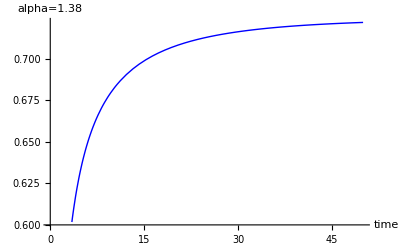

```mathematica
"Step Solution"
a=1.38;
x0=0;
Xin=UnitStep[t];
Yin=EXP[-50*t^2];
diffsol=NDSolve[{x1'[t]==x0-(1+a)*x1[t]+a*x2[t],
x2'[t]==x1[t]-(1+a)*x2[t]+a*x3[t],
x3'[t]==x2[t]-(1+a)*x3[t]+a*x4[t],
x4'[t]==x3[t]-(1+a)*x4[t]+a*x5[t],
x5'[t]==x4[t]-(1+a)*x5[t]+a*x6[t],
x6'[t]==x5[t]-(1+a)*x6[t]+a*x7[t],
x7'[t]==x6[t]-(1+a)*x7[t]+a*x8[t],
x8'[t]==x7[t]-(1+a)*x8[t]+a*x9[t],
x9'[t]==x8[t]-(1+a)*x9[t]+a*x10[t],
x10'[t]==x9[t]-(1+a)*x10[t]+a*x11[t],
x11'[t]==x10[t]-(1+a)*x11[t]+a*x12[t],
x12'[t]==x11[t]-(1+a)*x12[t]+a*x13[t],
x13'[t]==x12[t]-(1+a)*x13[t]+a*x14[t],
x14'[t]==x13[t]-(1+a)*x14[t]+a*x15[t],
x15'[t]==x14[t]-(1+a)*x15[t]+a*x16[t],
x16'[t]==x15[t]-(1+a)*x16[t]+a*x17[t],
x17'[t]==x16[t]-(1+a)*x17[t]+a*x18[t],
x18'[t]==x17[t]-(1+a)*x18[t]+a*x19[t],
x19'[t]==x18[t]-(1+a)*x19[t]+a*x20[t],
x20'[t]==x19[t]-(1+a)*x20[t]+Xin,x1[0]==0,x2[0]==0,x3[0]==0,x4[0]==0,x5[0]==0,x6[0]==0,x7[0]==0,x8[0]==0,x9[0]==0,x10[0]==0,x11[0]==0,x12[0]==0,x13[0]==0,x14[0]==0,x15[0]==0,x16[0]==0,x17[0]==0,x18[0]==0,x19[0]==0,x20[0]==0},{x1[t],x2[t],x3[t],x4[t],x5[t],x6[t],x7[t],x8[t],x9[t],x10[t],x11[t],x12[t],x13[t],x14[t],x15[t],x16[t],x17[t],x18[t],x19[t],x20[t]},{t,0,200}];

{x1out[t_],x2out[t_],x3out[t_],x4out[t_],x5out[t_],x6out[t_],x7out[t_],x8out[t_],x9out[t_],x10out[t_],x11out[t_],x12out[t_],x13out[t_],x14out[t_],x15out[t_],x16out[t_],x17out[t_],x18out[t_],x19out[t_],x20out[t_]}={x1[t],x2[t],x3[t],x4[t],x5[t],x6[t],x7[t],x8[t],x9[t],x10[t],x11[t],x12[t],x13[t],x14[t],x15[t],x16[t],x17[t],x18[t],x19[t],x20[t]}/.Flatten[diffsol];
Plot[x20out[t],{t,0,50},AxesLabel->{"time","alpha=1.38","Response to Unit Step Perturbation"},PlotStyle->{RGBColor[0,0,1]}]
```

Step Solution

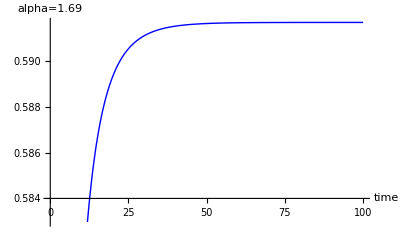

```mathematica
"Step Solution"
a=1.69;
x0=0;
Xin=UnitStep[t];
Yin=EXP[-50*t^2];
diffsol=NDSolve[{x1'[t]==x0-(1+a)*x1[t]+a*x2[t],
x2'[t]==x1[t]-(1+a)*x2[t]+a*x3[t],
x3'[t]==x2[t]-(1+a)*x3[t]+a*x4[t],
x4'[t]==x3[t]-(1+a)*x4[t]+a*x5[t],
x5'[t]==x4[t]-(1+a)*x5[t]+a*x6[t],
x6'[t]==x5[t]-(1+a)*x6[t]+a*x7[t],
x7'[t]==x6[t]-(1+a)*x7[t]+a*x8[t],
x8'[t]==x7[t]-(1+a)*x8[t]+a*x9[t],
x9'[t]==x8[t]-(1+a)*x9[t]+a*x10[t],
x10'[t]==x9[t]-(1+a)*x10[t]+a*x11[t],
x11'[t]==x10[t]-(1+a)*x11[t]+a*x12[t],
x12'[t]==x11[t]-(1+a)*x12[t]+a*x13[t],
x13'[t]==x12[t]-(1+a)*x13[t]+a*x14[t],
x14'[t]==x13[t]-(1+a)*x14[t]+a*x15[t],
x15'[t]==x14[t]-(1+a)*x15[t]+a*x16[t],
x16'[t]==x15[t]-(1+a)*x16[t]+a*x17[t],
x17'[t]==x16[t]-(1+a)*x17[t]+a*x18[t],
x18'[t]==x17[t]-(1+a)*x18[t]+a*x19[t],
x19'[t]==x18[t]-(1+a)*x19[t]+a*x20[t],
x20'[t]==x19[t]-(1+a)*x20[t]+Xin,x1[0]==0,x2[0]==0,x3[0]==0,x4[0]==0,x5[0]==0,x6[0]==0,x7[0]==0,x8[0]==0,x9[0]==0,x10[0]==0,x11[0]==0,x12[0]==0,x13[0]==0,x14[0]==0,x15[0]==0,x16[0]==0,x17[0]==0,x18[0]==0,x19[0]==0,x20[0]==0},{x1[t],x2[t],x3[t],x4[t],x5[t],x6[t],x7[t],x8[t],x9[t],x10[t],x11[t],x12[t],x13[t],x14[t],x15[t],x16[t],x17[t],x18[t],x19[t],x20[t]},{t,0,200}];

{x1out[t_],x2out[t_],x3out[t_],x4out[t_],x5out[t_],x6out[t_],x7out[t_],x8out[t_],x9out[t_],x10out[t_],x11out[t_],x12out[t_],x13out[t_],x14out[t_],x15out[t_],x16out[t_],x17out[t_],x18out[t_],x19out[t_],x20out[t_]}={x1[t],x2[t],x3[t],x4[t],x5[t],x6[t],x7[t],x8[t],x9[t],x10[t],x11[t],x12[t],x13[t],x14[t],x15[t],x16[t],x17[t],x18[t],x19[t],x20[t]}/.Flatten[diffsol];
Plot[x20out[t],{t,0,100},AxesLabel->{"time","alpha=1.69","Response to Unit Step Perturbation"},PlotStyle->{RGBColor[0,0,1]}]
```

Step Solution

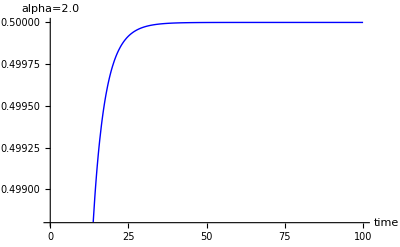

```mathematica
"Step Solution"
a=2.00;
x0=0;
Xin=UnitStep[t];
Yin=EXP[-50*t^2];
diffsol=NDSolve[{x1'[t]==x0-(1+a)*x1[t]+a*x2[t],
x2'[t]==x1[t]-(1+a)*x2[t]+a*x3[t],
x3'[t]==x2[t]-(1+a)*x3[t]+a*x4[t],
x4'[t]==x3[t]-(1+a)*x4[t]+a*x5[t],
x5'[t]==x4[t]-(1+a)*x5[t]+a*x6[t],
x6'[t]==x5[t]-(1+a)*x6[t]+a*x7[t],
x7'[t]==x6[t]-(1+a)*x7[t]+a*x8[t],
x8'[t]==x7[t]-(1+a)*x8[t]+a*x9[t],
x9'[t]==x8[t]-(1+a)*x9[t]+a*x10[t],
x10'[t]==x9[t]-(1+a)*x10[t]+a*x11[t],
x11'[t]==x10[t]-(1+a)*x11[t]+a*x12[t],
x12'[t]==x11[t]-(1+a)*x12[t]+a*x13[t],
x13'[t]==x12[t]-(1+a)*x13[t]+a*x14[t],
x14'[t]==x13[t]-(1+a)*x14[t]+a*x15[t],
x15'[t]==x14[t]-(1+a)*x15[t]+a*x16[t],
x16'[t]==x15[t]-(1+a)*x16[t]+a*x17[t],
x17'[t]==x16[t]-(1+a)*x17[t]+a*x18[t],
x18'[t]==x17[t]-(1+a)*x18[t]+a*x19[t],
x19'[t]==x18[t]-(1+a)*x19[t]+a*x20[t],
x20'[t]==x19[t]-(1+a)*x20[t]+Xin,x1[0]==0,x2[0]==0,x3[0]==0,x4[0]==0,x5[0]==0,x6[0]==0,x7[0]==0,x8[0]==0,x9[0]==0,x10[0]==0,x11[0]==0,x12[0]==0,x13[0]==0,x14[0]==0,x15[0]==0,x16[0]==0,x17[0]==0,x18[0]==0,x19[0]==0,x20[0]==0},{x1[t],x2[t],x3[t],x4[t],x5[t],x6[t],x7[t],x8[t],x9[t],x10[t],x11[t],x12[t],x13[t],x14[t],x15[t],x16[t],x17[t],x18[t],x19[t],x20[t]},{t,0,200}];

{x1out[t_],x2out[t_],x3out[t_],x4out[t_],x5out[t_],x6out[t_],x7out[t_],x8out[t_],x9out[t_],x10out[t_],x11out[t_],x12out[t_],x13out[t_],x14out[t_],x15out[t_],x16out[t_],x17out[t_],x18out[t_],x19out[t_],x20out[t_]}={x1[t],x2[t],x3[t],x4[t],x5[t],x6[t],x7[t],x8[t],x9[t],x10[t],x11[t],x12[t],x13[t],x14[t],x15[t],x16[t],x17[t],x18[t],x19[t],x20[t]}/.Flatten[diffsol];
Plot[x20out[t],{t,0,100},AxesLabel->{"time","alpha=2.0","Response to Unit Step Perturbation"},PlotStyle->{RGBColor[0,0,1]}]
```

Impule Solutions

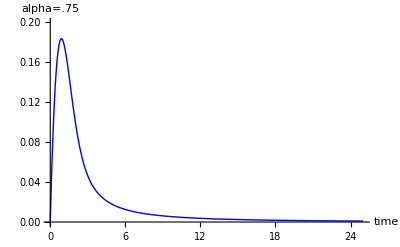

```mathematica
"Impulse Solutions"
a=0.75;
x0=0;
Xin=UnitStep[t];
Y=Sqrt[a/π]Exp[-a*t^2];
diffsol=NDSolve[{x1'[t]==x0-(1+a)*x1[t]+a*x2[t],
x2'[t]==x1[t]-(1+a)*x2[t]+a*x3[t],
x3'[t]==x2[t]-(1+a)*x3[t]+a*x4[t],
x4'[t]==x3[t]-(1+a)*x4[t]+a*x5[t],
x5'[t]==x4[t]-(1+a)*x5[t]+a*x6[t],
x6'[t]==x5[t]-(1+a)*x6[t]+a*x7[t],
x7'[t]==x6[t]-(1+a)*x7[t]+a*x8[t],
x8'[t]==x7[t]-(1+a)*x8[t]+a*x9[t],
x9'[t]==x8[t]-(1+a)*x9[t]+a*x10[t],
x10'[t]==x9[t]-(1+a)*x10[t]+a*x11[t],
x11'[t]==x10[t]-(1+a)*x11[t]+a*x12[t],
x12'[t]==x11[t]-(1+a)*x12[t]+a*x13[t],
x13'[t]==x12[t]-(1+a)*x13[t]+a*x14[t],
x14'[t]==x13[t]-(1+a)*x14[t]+a*x15[t],
x15'[t]==x14[t]-(1+a)*x15[t]+a*x16[t],
x16'[t]==x15[t]-(1+a)*x16[t]+a*x17[t],
x17'[t]==x16[t]-(1+a)*x17[t]+a*x18[t],
x18'[t]==x17[t]-(1+a)*x18[t]+a*x19[t],
x19'[t]==x18[t]-(1+a)*x19[t]+a*x20[t],
x20'[t]==x19[t]-(1+a)*x20[t]+Y,x1[0]==0,x2[0]==0,x3[0]==0,x4[0]==0,x5[0]==0,x6[0]==0,x7[0]==0,x8[0]==0,x9[0]==0,x10[0]==0,x11[0]==0,x12[0]==0,x13[0]==0,x14[0]==0,x15[0]==0,x16[0]==0,x17[0]==0,x18[0]==0,x19[0]==0,x20[0]==0},{x1[t],x2[t],x3[t],x4[t],x5[t],x6[t],x7[t],x8[t],x9[t],x10[t],x11[t],x12[t],x13[t],x14[t],x15[t],x16[t],x17[t],x18[t],x19[t],x20[t]},{t,0,200}];

{x1out[t_],x2out[t_],x3out[t_],x4out[t_],x5out[t_],x6out[t_],x7out[t_],x8out[t_],x9out[t_],x10out[t_],x11out[t_],x12out[t_],x13out[t_],x14out[t_],x15out[t_],x16out[t_],x17out[t_],x18out[t_],x19out[t_],x20out[t_]}={x1[t],x2[t],x3[t],x4[t],x5[t],x6[t],x7[t],x8[t],x9[t],x10[t],x11[t],x12[t],x13[t],x14[t],x15[t],x16[t],x17[t],x18[t],x19[t],x20[t]}/.Flatten[diffsol];
Plot[x20out[t],{t,0,25},AxesLabel->{"time","alpha=.75","Response to Unit Step Perturbation"},PlotStyle->{RGBColor[0,0,1]},PlotRange->{0,.20}]
```

Impule Solutions

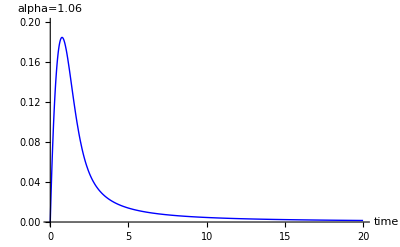

```mathematica
"Impulse Solutions"
a=1.06;
x0=0;
Xin=UnitStep[t];
Y=Sqrt[a/π]Exp[-a*t^2];
diffsol=NDSolve[{x1'[t]==x0-(1+a)*x1[t]+a*x2[t],
x2'[t]==x1[t]-(1+a)*x2[t]+a*x3[t],
x3'[t]==x2[t]-(1+a)*x3[t]+a*x4[t],
x4'[t]==x3[t]-(1+a)*x4[t]+a*x5[t],
x5'[t]==x4[t]-(1+a)*x5[t]+a*x6[t],
x6'[t]==x5[t]-(1+a)*x6[t]+a*x7[t],
x7'[t]==x6[t]-(1+a)*x7[t]+a*x8[t],
x8'[t]==x7[t]-(1+a)*x8[t]+a*x9[t],
x9'[t]==x8[t]-(1+a)*x9[t]+a*x10[t],
x10'[t]==x9[t]-(1+a)*x10[t]+a*x11[t],
x11'[t]==x10[t]-(1+a)*x11[t]+a*x12[t],
x12'[t]==x11[t]-(1+a)*x12[t]+a*x13[t],
x13'[t]==x12[t]-(1+a)*x13[t]+a*x14[t],
x14'[t]==x13[t]-(1+a)*x14[t]+a*x15[t],
x15'[t]==x14[t]-(1+a)*x15[t]+a*x16[t],
x16'[t]==x15[t]-(1+a)*x16[t]+a*x17[t],
x17'[t]==x16[t]-(1+a)*x17[t]+a*x18[t],
x18'[t]==x17[t]-(1+a)*x18[t]+a*x19[t],
x19'[t]==x18[t]-(1+a)*x19[t]+a*x20[t],
x20'[t]==x19[t]-(1+a)*x20[t]+Y,x1[0]==0,x2[0]==0,x3[0]==0,x4[0]==0,x5[0]==0,x6[0]==0,x7[0]==0,x8[0]==0,x9[0]==0,x10[0]==0,x11[0]==0,x12[0]==0,x13[0]==0,x14[0]==0,x15[0]==0,x16[0]==0,x17[0]==0,x18[0]==0,x19[0]==0,x20[0]==0},{x1[t],x2[t],x3[t],x4[t],x5[t],x6[t],x7[t],x8[t],x9[t],x10[t],x11[t],x12[t],x13[t],x14[t],x15[t],x16[t],x17[t],x18[t],x19[t],x20[t]},{t,0,200}];

{x1out[t_],x2out[t_],x3out[t_],x4out[t_],x5out[t_],x6out[t_],x7out[t_],x8out[t_],x9out[t_],x10out[t_],x11out[t_],x12out[t_],x13out[t_],x14out[t_],x15out[t_],x16out[t_],x17out[t_],x18out[t_],x19out[t_],x20out[t_]}={x1[t],x2[t],x3[t],x4[t],x5[t],x6[t],x7[t],x8[t],x9[t],x10[t],x11[t],x12[t],x13[t],x14[t],x15[t],x16[t],x17[t],x18[t],x19[t],x20[t]}/.Flatten[diffsol];
Plot[x20out[t],{t,0,20},AxesLabel->{"time","alpha=1.06","Response to Unit Step Perturbation"},PlotStyle->{RGBColor[0,0,1]},PlotRange->{0,.20}]
```

Impule Solutions

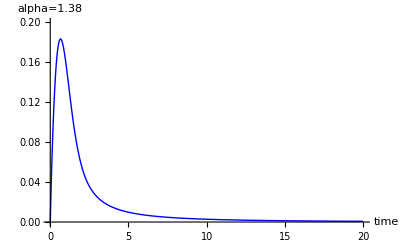

```mathematica
"Impulse Solutions"
a=1.38;
x0=0;
Xin=UnitStep[t];
Y=Sqrt[a/π]Exp[-a*t^2];
diffsol=NDSolve[{x1'[t]==x0-(1+a)*x1[t]+a*x2[t],
x2'[t]==x1[t]-(1+a)*x2[t]+a*x3[t],
x3'[t]==x2[t]-(1+a)*x3[t]+a*x4[t],
x4'[t]==x3[t]-(1+a)*x4[t]+a*x5[t],
x5'[t]==x4[t]-(1+a)*x5[t]+a*x6[t],
x6'[t]==x5[t]-(1+a)*x6[t]+a*x7[t],
x7'[t]==x6[t]-(1+a)*x7[t]+a*x8[t],
x8'[t]==x7[t]-(1+a)*x8[t]+a*x9[t],
x9'[t]==x8[t]-(1+a)*x9[t]+a*x10[t],
x10'[t]==x9[t]-(1+a)*x10[t]+a*x11[t],
x11'[t]==x10[t]-(1+a)*x11[t]+a*x12[t],
x12'[t]==x11[t]-(1+a)*x12[t]+a*x13[t],
x13'[t]==x12[t]-(1+a)*x13[t]+a*x14[t],
x14'[t]==x13[t]-(1+a)*x14[t]+a*x15[t],
x15'[t]==x14[t]-(1+a)*x15[t]+a*x16[t],
x16'[t]==x15[t]-(1+a)*x16[t]+a*x17[t],
x17'[t]==x16[t]-(1+a)*x17[t]+a*x18[t],
x18'[t]==x17[t]-(1+a)*x18[t]+a*x19[t],
x19'[t]==x18[t]-(1+a)*x19[t]+a*x20[t],
x20'[t]==x19[t]-(1+a)*x20[t]+Y,x1[0]==0,x2[0]==0,x3[0]==0,x4[0]==0,x5[0]==0,x6[0]==0,x7[0]==0,x8[0]==0,x9[0]==0,x10[0]==0,x11[0]==0,x12[0]==0,x13[0]==0,x14[0]==0,x15[0]==0,x16[0]==0,x17[0]==0,x18[0]==0,x19[0]==0,x20[0]==0},{x1[t],x2[t],x3[t],x4[t],x5[t],x6[t],x7[t],x8[t],x9[t],x10[t],x11[t],x12[t],x13[t],x14[t],x15[t],x16[t],x17[t],x18[t],x19[t],x20[t]},{t,0,200}];

{x1out[t_],x2out[t_],x3out[t_],x4out[t_],x5out[t_],x6out[t_],x7out[t_],x8out[t_],x9out[t_],x10out[t_],x11out[t_],x12out[t_],x13out[t_],x14out[t_],x15out[t_],x16out[t_],x17out[t_],x18out[t_],x19out[t_],x20out[t_]}={x1[t],x2[t],x3[t],x4[t],x5[t],x6[t],x7[t],x8[t],x9[t],x10[t],x11[t],x12[t],x13[t],x14[t],x15[t],x16[t],x17[t],x18[t],x19[t],x20[t]}/.Flatten[diffsol];
Plot[x20out[t],{t,0,20},AxesLabel->{"time","alpha=1.38","Response to Unit Step Perturbation"},PlotStyle->{RGBColor[0,0,1]},PlotRange->{0,.20}]
```

Impule Solutions

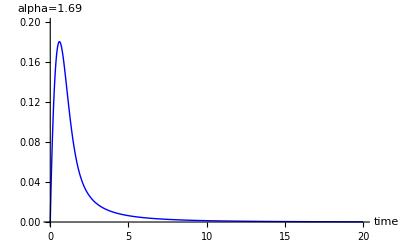

```mathematica
"Impulse Solutions"
a=1.69;
x0=0;
Xin=UnitStep[t];
Y=Sqrt[a/π]Exp[-a*t^2];
diffsol=NDSolve[{x1'[t]==x0-(1+a)*x1[t]+a*x2[t],
x2'[t]==x1[t]-(1+a)*x2[t]+a*x3[t],
x3'[t]==x2[t]-(1+a)*x3[t]+a*x4[t],
x4'[t]==x3[t]-(1+a)*x4[t]+a*x5[t],
x5'[t]==x4[t]-(1+a)*x5[t]+a*x6[t],
x6'[t]==x5[t]-(1+a)*x6[t]+a*x7[t],
x7'[t]==x6[t]-(1+a)*x7[t]+a*x8[t],
x8'[t]==x7[t]-(1+a)*x8[t]+a*x9[t],
x9'[t]==x8[t]-(1+a)*x9[t]+a*x10[t],
x10'[t]==x9[t]-(1+a)*x10[t]+a*x11[t],
x11'[t]==x10[t]-(1+a)*x11[t]+a*x12[t],
x12'[t]==x11[t]-(1+a)*x12[t]+a*x13[t],
x13'[t]==x12[t]-(1+a)*x13[t]+a*x14[t],
x14'[t]==x13[t]-(1+a)*x14[t]+a*x15[t],
x15'[t]==x14[t]-(1+a)*x15[t]+a*x16[t],
x16'[t]==x15[t]-(1+a)*x16[t]+a*x17[t],
x17'[t]==x16[t]-(1+a)*x17[t]+a*x18[t],
x18'[t]==x17[t]-(1+a)*x18[t]+a*x19[t],
x19'[t]==x18[t]-(1+a)*x19[t]+a*x20[t],
x20'[t]==x19[t]-(1+a)*x20[t]+Y,x1[0]==0,x2[0]==0,x3[0]==0,x4[0]==0,x5[0]==0,x6[0]==0,x7[0]==0,x8[0]==0,x9[0]==0,x10[0]==0,x11[0]==0,x12[0]==0,x13[0]==0,x14[0]==0,x15[0]==0,x16[0]==0,x17[0]==0,x18[0]==0,x19[0]==0,x20[0]==0},{x1[t],x2[t],x3[t],x4[t],x5[t],x6[t],x7[t],x8[t],x9[t],x10[t],x11[t],x12[t],x13[t],x14[t],x15[t],x16[t],x17[t],x18[t],x19[t],x20[t]},{t,0,200}];

{x1out[t_],x2out[t_],x3out[t_],x4out[t_],x5out[t_],x6out[t_],x7out[t_],x8out[t_],x9out[t_],x10out[t_],x11out[t_],x12out[t_],x13out[t_],x14out[t_],x15out[t_],x16out[t_],x17out[t_],x18out[t_],x19out[t_],x20out[t_]}={x1[t],x2[t],x3[t],x4[t],x5[t],x6[t],x7[t],x8[t],x9[t],x10[t],x11[t],x12[t],x13[t],x14[t],x15[t],x16[t],x17[t],x18[t],x19[t],x20[t]}/.Flatten[diffsol];
Plot[x20out[t],{t,0,20},AxesLabel->{"time","alpha=1.69","Response to Unit Step Perturbation"},PlotStyle->{RGBColor[0,0,1]},PlotRange->{0,.20}]
```

Impule Solutions

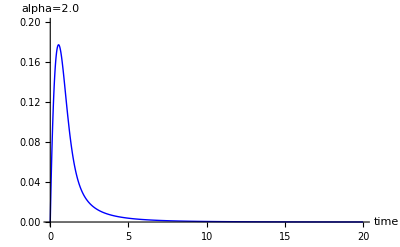

```mathematica
"Impulse Solutions"
a=2.0;
x0=0;
Xin=UnitStep[t];
Y=Sqrt[a/π]Exp[-a*t^2];
diffsol=NDSolve[{x1'[t]==x0-(1+a)*x1[t]+a*x2[t],
x2'[t]==x1[t]-(1+a)*x2[t]+a*x3[t],
x3'[t]==x2[t]-(1+a)*x3[t]+a*x4[t],
x4'[t]==x3[t]-(1+a)*x4[t]+a*x5[t],
x5'[t]==x4[t]-(1+a)*x5[t]+a*x6[t],
x6'[t]==x5[t]-(1+a)*x6[t]+a*x7[t],
x7'[t]==x6[t]-(1+a)*x7[t]+a*x8[t],
x8'[t]==x7[t]-(1+a)*x8[t]+a*x9[t],
x9'[t]==x8[t]-(1+a)*x9[t]+a*x10[t],
x10'[t]==x9[t]-(1+a)*x10[t]+a*x11[t],
x11'[t]==x10[t]-(1+a)*x11[t]+a*x12[t],
x12'[t]==x11[t]-(1+a)*x12[t]+a*x13[t],
x13'[t]==x12[t]-(1+a)*x13[t]+a*x14[t],
x14'[t]==x13[t]-(1+a)*x14[t]+a*x15[t],
x15'[t]==x14[t]-(1+a)*x15[t]+a*x16[t],
x16'[t]==x15[t]-(1+a)*x16[t]+a*x17[t],
x17'[t]==x16[t]-(1+a)*x17[t]+a*x18[t],
x18'[t]==x17[t]-(1+a)*x18[t]+a*x19[t],
x19'[t]==x18[t]-(1+a)*x19[t]+a*x20[t],
x20'[t]==x19[t]-(1+a)*x20[t]+Y,x1[0]==0,x2[0]==0,x3[0]==0,x4[0]==0,x5[0]==0,x6[0]==0,x7[0]==0,x8[0]==0,x9[0]==0,x10[0]==0,x11[0]==0,x12[0]==0,x13[0]==0,x14[0]==0,x15[0]==0,x16[0]==0,x17[0]==0,x18[0]==0,x19[0]==0,x20[0]==0},{x1[t],x2[t],x3[t],x4[t],x5[t],x6[t],x7[t],x8[t],x9[t],x10[t],x11[t],x12[t],x13[t],x14[t],x15[t],x16[t],x17[t],x18[t],x19[t],x20[t]},{t,0,200}];

{x1out[t_],x2out[t_],x3out[t_],x4out[t_],x5out[t_],x6out[t_],x7out[t_],x8out[t_],x9out[t_],x10out[t_],x11out[t_],x12out[t_],x13out[t_],x14out[t_],x15out[t_],x16out[t_],x17out[t_],x18out[t_],x19out[t_],x20out[t_]}={x1[t],x2[t],x3[t],x4[t],x5[t],x6[t],x7[t],x8[t],x9[t],x10[t],x11[t],x12[t],x13[t],x14[t],x15[t],x16[t],x17[t],x18[t],x19[t],x20[t]}/.Flatten[diffsol];
Plot[x20out[t],{t,0,20},AxesLabel->{"time","alpha=2.0","Response to Unit Step Perturbation"},PlotStyle->{RGBColor[0,0,1]},PlotRange->{0,.20}]
```

```mathematica
"Perturbations in the Liquid Inlet Concentrations"
```

PART II: Perturbations in the Tops Vapor Concentration

Step Solution

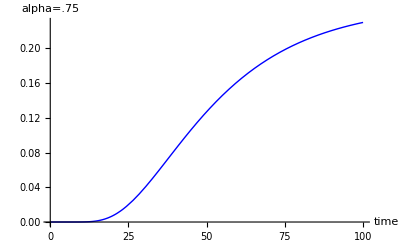

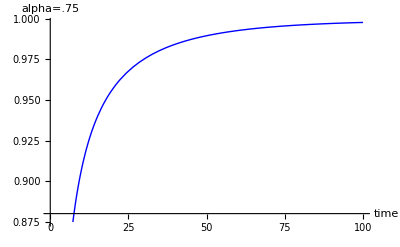

```mathematica
"PART II: Perturbations in the Tops Vapor Concentration"
"Step Solution"
a=0.75;
x0=0;
Xin=UnitStep[t];
Yin=EXP[-50*t^2];
diffsol=NDSolve[{x1'[t]==Xin-(1+a)*x1[t]+a*x2[t],
x2'[t]==x1[t]-(1+a)*x2[t]+a*x3[t],
x3'[t]==x2[t]-(1+a)*x3[t]+a*x4[t],
x4'[t]==x3[t]-(1+a)*x4[t]+a*x5[t],
x5'[t]==x4[t]-(1+a)*x5[t]+a*x6[t],
x6'[t]==x5[t]-(1+a)*x6[t]+a*x7[t],
x7'[t]==x6[t]-(1+a)*x7[t]+a*x8[t],
x8'[t]==x7[t]-(1+a)*x8[t]+a*x9[t],
x9'[t]==x8[t]-(1+a)*x9[t]+a*x10[t],
x10'[t]==x9[t]-(1+a)*x10[t]+a*x11[t],
x11'[t]==x10[t]-(1+a)*x11[t]+a*x12[t],
x12'[t]==x11[t]-(1+a)*x12[t]+a*x13[t],
x13'[t]==x12[t]-(1+a)*x13[t]+a*x14[t],
x14'[t]==x13[t]-(1+a)*x14[t]+a*x15[t],
x15'[t]==x14[t]-(1+a)*x15[t]+a*x16[t],
x16'[t]==x15[t]-(1+a)*x16[t]+a*x17[t],
x17'[t]==x16[t]-(1+a)*x17[t]+a*x18[t],
x18'[t]==x17[t]-(1+a)*x18[t]+a*x19[t],
x19'[t]==x18[t]-(1+a)*x19[t]+a*x20[t],
x20'[t]==x19[t]-(1+a)*x20[t],x1[0]==0,x2[0]==0,x3[0]==0,x4[0]==0,x5[0]==0,x6[0]==0,x7[0]==0,x8[0]==0,x9[0]==0,x10[0]==0,x11[0]==0,x12[0]==0,x13[0]==0,x14[0]==0,x15[0]==0,x16[0]==0,x17[0]==0,x18[0]==0,x19[0]==0,x20[0]==0},{x1[t],x2[t],x3[t],x4[t],x5[t],x6[t],x7[t],x8[t],x9[t],x10[t],x11[t],x12[t],x13[t],x14[t],x15[t],x16[t],x17[t],x18[t],x19[t],x20[t]},{t,0,200}];

{x1out[t_],x2out[t_],x3out[t_],x4out[t_],x5out[t_],x6out[t_],x7out[t_],x8out[t_],x9out[t_],x10out[t_],x11out[t_],x12out[t_],x13out[t_],x14out[t_],x15out[t_],x16out[t_],x17out[t_],x18out[t_],x19out[t_],x20out[t_]}={x1[t],x2[t],x3[t],x4[t],x5[t],x6[t],x7[t],x8[t],x9[t],x10[t],x11[t],x12[t],x13[t],x14[t],x15[t],x16[t],x17[t],x18[t],x19[t],x20[t]}/.Flatten[diffsol];
Plot[x20out[t],{t,0,100},AxesLabel->{"time","alpha=.75","Response to Unit Step Perturbation"},PlotStyle->{RGBColor[0,0,1]}]
Plot[x1out[t],{t,0,100},AxesLabel->{"time","alpha=.75","Response to Unit Step Perturbation"},PlotStyle->{RGBColor[0,0,1]}]
```

Step Solution

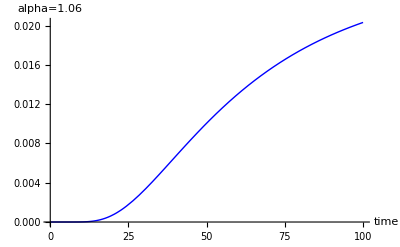

```mathematica
"Step Solution"
a=1.06;
x0=0;
Xin=UnitStep[t];
Yin=EXP[-50*t^2];
diffsol=NDSolve[{x1'[t]==Xin-(1+a)*x1[t]+a*x2[t],
x2'[t]==x1[t]-(1+a)*x2[t]+a*x3[t],
x3'[t]==x2[t]-(1+a)*x3[t]+a*x4[t],
x4'[t]==x3[t]-(1+a)*x4[t]+a*x5[t],
x5'[t]==x4[t]-(1+a)*x5[t]+a*x6[t],
x6'[t]==x5[t]-(1+a)*x6[t]+a*x7[t],
x7'[t]==x6[t]-(1+a)*x7[t]+a*x8[t],
x8'[t]==x7[t]-(1+a)*x8[t]+a*x9[t],
x9'[t]==x8[t]-(1+a)*x9[t]+a*x10[t],
x10'[t]==x9[t]-(1+a)*x10[t]+a*x11[t],
x11'[t]==x10[t]-(1+a)*x11[t]+a*x12[t],
x12'[t]==x11[t]-(1+a)*x12[t]+a*x13[t],
x13'[t]==x12[t]-(1+a)*x13[t]+a*x14[t],
x14'[t]==x13[t]-(1+a)*x14[t]+a*x15[t],
x15'[t]==x14[t]-(1+a)*x15[t]+a*x16[t],
x16'[t]==x15[t]-(1+a)*x16[t]+a*x17[t],
x17'[t]==x16[t]-(1+a)*x17[t]+a*x18[t],
x18'[t]==x17[t]-(1+a)*x18[t]+a*x19[t],
x19'[t]==x18[t]-(1+a)*x19[t]+a*x20[t],
x20'[t]==x19[t]-(1+a)*x20[t],x1[0]==0,x2[0]==0,x3[0]==0,x4[0]==0,x5[0]==0,x6[0]==0,x7[0]==0,x8[0]==0,x9[0]==0,x10[0]==0,x11[0]==0,x12[0]==0,x13[0]==0,x14[0]==0,x15[0]==0,x16[0]==0,x17[0]==0,x18[0]==0,x19[0]==0,x20[0]==0},{x1[t],x2[t],x3[t],x4[t],x5[t],x6[t],x7[t],x8[t],x9[t],x10[t],x11[t],x12[t],x13[t],x14[t],x15[t],x16[t],x17[t],x18[t],x19[t],x20[t]},{t,0,200}];

{x1out[t_],x2out[t_],x3out[t_],x4out[t_],x5out[t_],x6out[t_],x7out[t_],x8out[t_],x9out[t_],x10out[t_],x11out[t_],x12out[t_],x13out[t_],x14out[t_],x15out[t_],x16out[t_],x17out[t_],x18out[t_],x19out[t_],x20out[t_]}={x1[t],x2[t],x3[t],x4[t],x5[t],x6[t],x7[t],x8[t],x9[t],x10[t],x11[t],x12[t],x13[t],x14[t],x15[t],x16[t],x17[t],x18[t],x19[t],x20[t]}/.Flatten[diffsol];
Plot[x20out[t],{t,0,100},AxesLabel->{"time","alpha=1.06","Response to Unit Step Perturbation"},PlotStyle->{RGBColor[0,0,1]}]
```

Step Solution

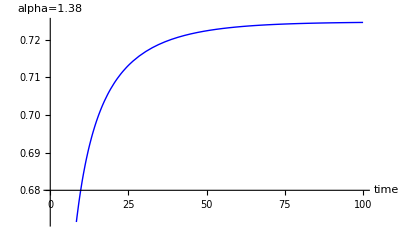

```mathematica
"Step Solution"
a=1.38;
x0=0;
Xin=UnitStep[t];
Yin=EXP[-50*t^2];
diffsol=NDSolve[{x1'[t]==Xin-(1+a)*x1[t]+a*x2[t],
x2'[t]==x1[t]-(1+a)*x2[t]+a*x3[t],
x3'[t]==x2[t]-(1+a)*x3[t]+a*x4[t],
x4'[t]==x3[t]-(1+a)*x4[t]+a*x5[t],
x5'[t]==x4[t]-(1+a)*x5[t]+a*x6[t],
x6'[t]==x5[t]-(1+a)*x6[t]+a*x7[t],
x7'[t]==x6[t]-(1+a)*x7[t]+a*x8[t],
x8'[t]==x7[t]-(1+a)*x8[t]+a*x9[t],
x9'[t]==x8[t]-(1+a)*x9[t]+a*x10[t],
x10'[t]==x9[t]-(1+a)*x10[t]+a*x11[t],
x11'[t]==x10[t]-(1+a)*x11[t]+a*x12[t],
x12'[t]==x11[t]-(1+a)*x12[t]+a*x13[t],
x13'[t]==x12[t]-(1+a)*x13[t]+a*x14[t],
x14'[t]==x13[t]-(1+a)*x14[t]+a*x15[t],
x15'[t]==x14[t]-(1+a)*x15[t]+a*x16[t],
x16'[t]==x15[t]-(1+a)*x16[t]+a*x17[t],
x17'[t]==x16[t]-(1+a)*x17[t]+a*x18[t],
x18'[t]==x17[t]-(1+a)*x18[t]+a*x19[t],
x19'[t]==x18[t]-(1+a)*x19[t]+a*x20[t],
x20'[t]==x19[t]-(1+a)*x20[t]+Xin,x1[0]==0,x2[0]==0,x3[0]==0,x4[0]==0,x5[0]==0,x6[0]==0,x7[0]==0,x8[0]==0,x9[0]==0,x10[0]==0,x11[0]==0,x12[0]==0,x13[0]==0,x14[0]==0,x15[0]==0,x16[0]==0,x17[0]==0,x18[0]==0,x19[0]==0,x20[0]==0},{x1[t],x2[t],x3[t],x4[t],x5[t],x6[t],x7[t],x8[t],x9[t],x10[t],x11[t],x12[t],x13[t],x14[t],x15[t],x16[t],x17[t],x18[t],x19[t],x20[t]},{t,0,200}];

{x1out[t_],x2out[t_],x3out[t_],x4out[t_],x5out[t_],x6out[t_],x7out[t_],x8out[t_],x9out[t_],x10out[t_],x11out[t_],x12out[t_],x13out[t_],x14out[t_],x15out[t_],x16out[t_],x17out[t_],x18out[t_],x19out[t_],x20out[t_]}={x1[t],x2[t],x3[t],x4[t],x5[t],x6[t],x7[t],x8[t],x9[t],x10[t],x11[t],x12[t],x13[t],x14[t],x15[t],x16[t],x17[t],x18[t],x19[t],x20[t]}/.Flatten[diffsol];
Plot[x20out[t],{t,0,100},AxesLabel->{"time","alpha=1.38","Response to Unit Step Perturbation"},PlotStyle->{RGBColor[0,0,1]}]
```

Step Solution

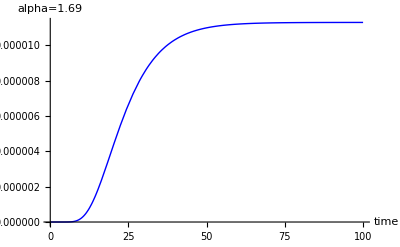

```mathematica
"Step Solution"
a=1.69;
x0=0;
Xin=UnitStep[t];
Yin=EXP[-50*t^2];
diffsol=NDSolve[{x1'[t]==Xin-(1+a)*x1[t]+a*x2[t],
x2'[t]==x1[t]-(1+a)*x2[t]+a*x3[t],
x3'[t]==x2[t]-(1+a)*x3[t]+a*x4[t],
x4'[t]==x3[t]-(1+a)*x4[t]+a*x5[t],
x5'[t]==x4[t]-(1+a)*x5[t]+a*x6[t],
x6'[t]==x5[t]-(1+a)*x6[t]+a*x7[t],
x7'[t]==x6[t]-(1+a)*x7[t]+a*x8[t],
x8'[t]==x7[t]-(1+a)*x8[t]+a*x9[t],
x9'[t]==x8[t]-(1+a)*x9[t]+a*x10[t],
x10'[t]==x9[t]-(1+a)*x10[t]+a*x11[t],
x11'[t]==x10[t]-(1+a)*x11[t]+a*x12[t],
x12'[t]==x11[t]-(1+a)*x12[t]+a*x13[t],
x13'[t]==x12[t]-(1+a)*x13[t]+a*x14[t],
x14'[t]==x13[t]-(1+a)*x14[t]+a*x15[t],
x15'[t]==x14[t]-(1+a)*x15[t]+a*x16[t],
x16'[t]==x15[t]-(1+a)*x16[t]+a*x17[t],
x17'[t]==x16[t]-(1+a)*x17[t]+a*x18[t],
x18'[t]==x17[t]-(1+a)*x18[t]+a*x19[t],
x19'[t]==x18[t]-(1+a)*x19[t]+a*x20[t],
x20'[t]==x19[t]-(1+a)*x20[t],x1[0]==0,x2[0]==0,x3[0]==0,x4[0]==0,x5[0]==0,x6[0]==0,x7[0]==0,x8[0]==0,x9[0]==0,x10[0]==0,x11[0]==0,x12[0]==0,x13[0]==0,x14[0]==0,x15[0]==0,x16[0]==0,x17[0]==0,x18[0]==0,x19[0]==0,x20[0]==0},{x1[t],x2[t],x3[t],x4[t],x5[t],x6[t],x7[t],x8[t],x9[t],x10[t],x11[t],x12[t],x13[t],x14[t],x15[t],x16[t],x17[t],x18[t],x19[t],x20[t]},{t,0,200}];

{x1out[t_],x2out[t_],x3out[t_],x4out[t_],x5out[t_],x6out[t_],x7out[t_],x8out[t_],x9out[t_],x10out[t_],x11out[t_],x12out[t_],x13out[t_],x14out[t_],x15out[t_],x16out[t_],x17out[t_],x18out[t_],x19out[t_],x20out[t_]}={x1[t],x2[t],x3[t],x4[t],x5[t],x6[t],x7[t],x8[t],x9[t],x10[t],x11[t],x12[t],x13[t],x14[t],x15[t],x16[t],x17[t],x18[t],x19[t],x20[t]}/.Flatten[diffsol];
Plot[x20out[t],{t,0,100},AxesLabel->{"time","alpha=1.69","Response to Unit Step Perturbation"},PlotStyle->{RGBColor[0,0,1]}]
```

Step Solution

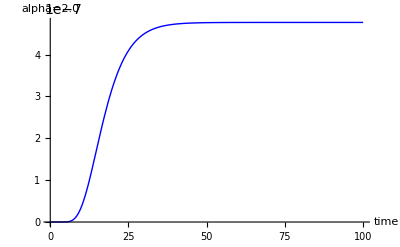

```mathematica
"Step Solution"
a=2.00;
x0=0;
Xin=UnitStep[t];
Yin=EXP[-50*t^2];
diffsol=NDSolve[{x1'[t]==Xin-(1+a)*x1[t]+a*x2[t],
x2'[t]==x1[t]-(1+a)*x2[t]+a*x3[t],
x3'[t]==x2[t]-(1+a)*x3[t]+a*x4[t],
x4'[t]==x3[t]-(1+a)*x4[t]+a*x5[t],
x5'[t]==x4[t]-(1+a)*x5[t]+a*x6[t],
x6'[t]==x5[t]-(1+a)*x6[t]+a*x7[t],
x7'[t]==x6[t]-(1+a)*x7[t]+a*x8[t],
x8'[t]==x7[t]-(1+a)*x8[t]+a*x9[t],
x9'[t]==x8[t]-(1+a)*x9[t]+a*x10[t],
x10'[t]==x9[t]-(1+a)*x10[t]+a*x11[t],
x11'[t]==x10[t]-(1+a)*x11[t]+a*x12[t],
x12'[t]==x11[t]-(1+a)*x12[t]+a*x13[t],
x13'[t]==x12[t]-(1+a)*x13[t]+a*x14[t],
x14'[t]==x13[t]-(1+a)*x14[t]+a*x15[t],
x15'[t]==x14[t]-(1+a)*x15[t]+a*x16[t],
x16'[t]==x15[t]-(1+a)*x16[t]+a*x17[t],
x17'[t]==x16[t]-(1+a)*x17[t]+a*x18[t],
x18'[t]==x17[t]-(1+a)*x18[t]+a*x19[t],
x19'[t]==x18[t]-(1+a)*x19[t]+a*x20[t],
x20'[t]==x19[t]-(1+a)*x20[t],x1[0]==0,x2[0]==0,x3[0]==0,x4[0]==0,x5[0]==0,x6[0]==0,x7[0]==0,x8[0]==0,x9[0]==0,x10[0]==0,x11[0]==0,x12[0]==0,x13[0]==0,x14[0]==0,x15[0]==0,x16[0]==0,x17[0]==0,x18[0]==0,x19[0]==0,x20[0]==0},{x1[t],x2[t],x3[t],x4[t],x5[t],x6[t],x7[t],x8[t],x9[t],x10[t],x11[t],x12[t],x13[t],x14[t],x15[t],x16[t],x17[t],x18[t],x19[t],x20[t]},{t,0,200}];

{x1out[t_],x2out[t_],x3out[t_],x4out[t_],x5out[t_],x6out[t_],x7out[t_],x8out[t_],x9out[t_],x10out[t_],x11out[t_],x12out[t_],x13out[t_],x14out[t_],x15out[t_],x16out[t_],x17out[t_],x18out[t_],x19out[t_],x20out[t_]}={x1[t],x2[t],x3[t],x4[t],x5[t],x6[t],x7[t],x8[t],x9[t],x10[t],x11[t],x12[t],x13[t],x14[t],x15[t],x16[t],x17[t],x18[t],x19[t],x20[t]}/.Flatten[diffsol];
Plot[x20out[t],{t,0,100},AxesLabel->{"time","alpha=2.0","Response to Unit Step Perturbation"},PlotStyle->{RGBColor[0,0,1]}]
```

Impulse Solutions

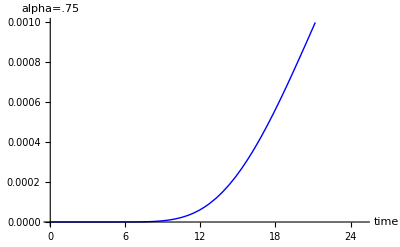

```mathematica
"Impulse Solutions"
a=0.75;
x0=0;
Xin=UnitStep[t];
Y=Sqrt[a/π]Exp[-a*t^2];
diffsol=NDSolve[{x1'[t]==Y-(1+a)*x1[t]+a*x2[t],
x2'[t]==x1[t]-(1+a)*x2[t]+a*x3[t],
x3'[t]==x2[t]-(1+a)*x3[t]+a*x4[t],
x4'[t]==x3[t]-(1+a)*x4[t]+a*x5[t],
x5'[t]==x4[t]-(1+a)*x5[t]+a*x6[t],
x6'[t]==x5[t]-(1+a)*x6[t]+a*x7[t],
x7'[t]==x6[t]-(1+a)*x7[t]+a*x8[t],
x8'[t]==x7[t]-(1+a)*x8[t]+a*x9[t],
x9'[t]==x8[t]-(1+a)*x9[t]+a*x10[t],
x10'[t]==x9[t]-(1+a)*x10[t]+a*x11[t],
x11'[t]==x10[t]-(1+a)*x11[t]+a*x12[t],
x12'[t]==x11[t]-(1+a)*x12[t]+a*x13[t],
x13'[t]==x12[t]-(1+a)*x13[t]+a*x14[t],
x14'[t]==x13[t]-(1+a)*x14[t]+a*x15[t],
x15'[t]==x14[t]-(1+a)*x15[t]+a*x16[t],
x16'[t]==x15[t]-(1+a)*x16[t]+a*x17[t],
x17'[t]==x16[t]-(1+a)*x17[t]+a*x18[t],
x18'[t]==x17[t]-(1+a)*x18[t]+a*x19[t],
x19'[t]==x18[t]-(1+a)*x19[t]+a*x20[t],
x20'[t]==x19[t]-(1+a)*x20[t],x1[0]==0,x2[0]==0,x3[0]==0,x4[0]==0,x5[0]==0,x6[0]==0,x7[0]==0,x8[0]==0,x9[0]==0,x10[0]==0,x11[0]==0,x12[0]==0,x13[0]==0,x14[0]==0,x15[0]==0,x16[0]==0,x17[0]==0,x18[0]==0,x19[0]==0,x20[0]==0},{x1[t],x2[t],x3[t],x4[t],x5[t],x6[t],x7[t],x8[t],x9[t],x10[t],x11[t],x12[t],x13[t],x14[t],x15[t],x16[t],x17[t],x18[t],x19[t],x20[t]},{t,0,200}];

{x1out[t_],x2out[t_],x3out[t_],x4out[t_],x5out[t_],x6out[t_],x7out[t_],x8out[t_],x9out[t_],x10out[t_],x11out[t_],x12out[t_],x13out[t_],x14out[t_],x15out[t_],x16out[t_],x17out[t_],x18out[t_],x19out[t_],x20out[t_]}={x1[t],x2[t],x3[t],x4[t],x5[t],x6[t],x7[t],x8[t],x9[t],x10[t],x11[t],x12[t],x13[t],x14[t],x15[t],x16[t],x17[t],x18[t],x19[t],x20[t]}/.Flatten[diffsol];
Plot[x20out[t],{t,0,25},AxesLabel->{"time","alpha=.75","Response to Unit Step Perturbation"},PlotStyle->{RGBColor[0,0,1]},PlotRange->{0,.001}]
```

Impule Solutions

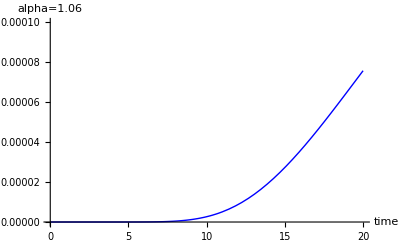

```mathematica
"Impulse Solutions"
a=1.06;
x0=0;
Xin=UnitStep[t];
Y=Sqrt[a/π]Exp[-a*t^2];
diffsol=NDSolve[{x1'[t]==Y-(1+a)*x1[t]+a*x2[t],
x2'[t]==x1[t]-(1+a)*x2[t]+a*x3[t],
x3'[t]==x2[t]-(1+a)*x3[t]+a*x4[t],
x4'[t]==x3[t]-(1+a)*x4[t]+a*x5[t],
x5'[t]==x4[t]-(1+a)*x5[t]+a*x6[t],
x6'[t]==x5[t]-(1+a)*x6[t]+a*x7[t],
x7'[t]==x6[t]-(1+a)*x7[t]+a*x8[t],
x8'[t]==x7[t]-(1+a)*x8[t]+a*x9[t],
x9'[t]==x8[t]-(1+a)*x9[t]+a*x10[t],
x10'[t]==x9[t]-(1+a)*x10[t]+a*x11[t],
x11'[t]==x10[t]-(1+a)*x11[t]+a*x12[t],
x12'[t]==x11[t]-(1+a)*x12[t]+a*x13[t],
x13'[t]==x12[t]-(1+a)*x13[t]+a*x14[t],
x14'[t]==x13[t]-(1+a)*x14[t]+a*x15[t],
x15'[t]==x14[t]-(1+a)*x15[t]+a*x16[t],
x16'[t]==x15[t]-(1+a)*x16[t]+a*x17[t],
x17'[t]==x16[t]-(1+a)*x17[t]+a*x18[t],
x18'[t]==x17[t]-(1+a)*x18[t]+a*x19[t],
x19'[t]==x18[t]-(1+a)*x19[t]+a*x20[t],
x20'[t]==x19[t]-(1+a)*x20[t],x1[0]==0,x2[0]==0,x3[0]==0,x4[0]==0,x5[0]==0,x6[0]==0,x7[0]==0,x8[0]==0,x9[0]==0,x10[0]==0,x11[0]==0,x12[0]==0,x13[0]==0,x14[0]==0,x15[0]==0,x16[0]==0,x17[0]==0,x18[0]==0,x19[0]==0,x20[0]==0},{x1[t],x2[t],x3[t],x4[t],x5[t],x6[t],x7[t],x8[t],x9[t],x10[t],x11[t],x12[t],x13[t],x14[t],x15[t],x16[t],x17[t],x18[t],x19[t],x20[t]},{t,0,200}];

{x1out[t_],x2out[t_],x3out[t_],x4out[t_],x5out[t_],x6out[t_],x7out[t_],x8out[t_],x9out[t_],x10out[t_],x11out[t_],x12out[t_],x13out[t_],x14out[t_],x15out[t_],x16out[t_],x17out[t_],x18out[t_],x19out[t_],x20out[t_]}={x1[t],x2[t],x3[t],x4[t],x5[t],x6[t],x7[t],x8[t],x9[t],x10[t],x11[t],x12[t],x13[t],x14[t],x15[t],x16[t],x17[t],x18[t],x19[t],x20[t]}/.Flatten[diffsol];
Plot[x20out[t],{t,0,20},AxesLabel->{"time","alpha=1.06","Response to Unit Step Perturbation"},PlotStyle->{RGBColor[0,0,1]},PlotRange->{0,.0001}]
```

Impulse Solutions

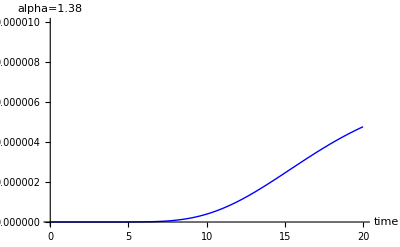

```mathematica
"Impulse Solutions"
a=1.38;
x0=0;
Xin=UnitStep[t];
Y=Sqrt[a/π]Exp[-a*t^2];
diffsol=NDSolve[{x1'[t]==Y-(1+a)*x1[t]+a*x2[t],
x2'[t]==x1[t]-(1+a)*x2[t]+a*x3[t],
x3'[t]==x2[t]-(1+a)*x3[t]+a*x4[t],
x4'[t]==x3[t]-(1+a)*x4[t]+a*x5[t],
x5'[t]==x4[t]-(1+a)*x5[t]+a*x6[t],
x6'[t]==x5[t]-(1+a)*x6[t]+a*x7[t],
x7'[t]==x6[t]-(1+a)*x7[t]+a*x8[t],
x8'[t]==x7[t]-(1+a)*x8[t]+a*x9[t],
x9'[t]==x8[t]-(1+a)*x9[t]+a*x10[t],
x10'[t]==x9[t]-(1+a)*x10[t]+a*x11[t],
x11'[t]==x10[t]-(1+a)*x11[t]+a*x12[t],
x12'[t]==x11[t]-(1+a)*x12[t]+a*x13[t],
x13'[t]==x12[t]-(1+a)*x13[t]+a*x14[t],
x14'[t]==x13[t]-(1+a)*x14[t]+a*x15[t],
x15'[t]==x14[t]-(1+a)*x15[t]+a*x16[t],
x16'[t]==x15[t]-(1+a)*x16[t]+a*x17[t],
x17'[t]==x16[t]-(1+a)*x17[t]+a*x18[t],
x18'[t]==x17[t]-(1+a)*x18[t]+a*x19[t],
x19'[t]==x18[t]-(1+a)*x19[t]+a*x20[t],
x20'[t]==x19[t]-(1+a)*x20[t],x1[0]==0,x2[0]==0,x3[0]==0,x4[0]==0,x5[0]==0,x6[0]==0,x7[0]==0,x8[0]==0,x9[0]==0,x10[0]==0,x11[0]==0,x12[0]==0,x13[0]==0,x14[0]==0,x15[0]==0,x16[0]==0,x17[0]==0,x18[0]==0,x19[0]==0,x20[0]==0},{x1[t],x2[t],x3[t],x4[t],x5[t],x6[t],x7[t],x8[t],x9[t],x10[t],x11[t],x12[t],x13[t],x14[t],x15[t],x16[t],x17[t],x18[t],x19[t],x20[t]},{t,0,200}];

{x1out[t_],x2out[t_],x3out[t_],x4out[t_],x5out[t_],x6out[t_],x7out[t_],x8out[t_],x9out[t_],x10out[t_],x11out[t_],x12out[t_],x13out[t_],x14out[t_],x15out[t_],x16out[t_],x17out[t_],x18out[t_],x19out[t_],x20out[t_]}={x1[t],x2[t],x3[t],x4[t],x5[t],x6[t],x7[t],x8[t],x9[t],x10[t],x11[t],x12[t],x13[t],x14[t],x15[t],x16[t],x17[t],x18[t],x19[t],x20[t]}/.Flatten[diffsol];
Plot[x20out[t],{t,0,20},AxesLabel->{"time","alpha=1.38","Response to Unit Step Perturbation"},PlotStyle->{RGBColor[0,0,1]},PlotRange->{0,.00001}]
```

Impulse Solutions

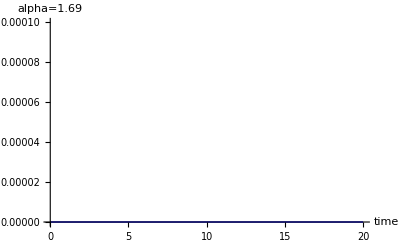

```mathematica
"Impulse Solutions"
a=1.69;
x0=0;
Xin=UnitStep[t];
Y=Sqrt[a/π]Exp[-a*t^2];
diffsol=NDSolve[{x1'[t]==x0-(1+a)*x1[t]+a*x2[t],
x2'[t]==x1[t]-(1+a)*x2[t]+a*x3[t],
x3'[t]==x2[t]-(1+a)*x3[t]+a*x4[t],
x4'[t]==x3[t]-(1+a)*x4[t]+a*x5[t],
x5'[t]==x4[t]-(1+a)*x5[t]+a*x6[t],
x6'[t]==x5[t]-(1+a)*x6[t]+a*x7[t],
x7'[t]==x6[t]-(1+a)*x7[t]+a*x8[t],
x8'[t]==x7[t]-(1+a)*x8[t]+a*x9[t],
x9'[t]==x8[t]-(1+a)*x9[t]+a*x10[t],
x10'[t]==x9[t]-(1+a)*x10[t]+a*x11[t],
x11'[t]==x10[t]-(1+a)*x11[t]+a*x12[t],
x12'[t]==x11[t]-(1+a)*x12[t]+a*x13[t],
x13'[t]==x12[t]-(1+a)*x13[t]+a*x14[t],
x14'[t]==x13[t]-(1+a)*x14[t]+a*x15[t],
x15'[t]==x14[t]-(1+a)*x15[t]+a*x16[t],
x16'[t]==x15[t]-(1+a)*x16[t]+a*x17[t],
x17'[t]==x16[t]-(1+a)*x17[t]+a*x18[t],
x18'[t]==x17[t]-(1+a)*x18[t]+a*x19[t],
x19'[t]==x18[t]-(1+a)*x19[t]+a*x20[t],
x20'[t]==x19[t]-(1+a)*x20[t],x1[0]==0,x2[0]==0,x3[0]==0,x4[0]==0,x5[0]==0,x6[0]==0,x7[0]==0,x8[0]==0,x9[0]==0,x10[0]==0,x11[0]==0,x12[0]==0,x13[0]==0,x14[0]==0,x15[0]==0,x16[0]==0,x17[0]==0,x18[0]==0,x19[0]==0,x20[0]==0},{x1[t],x2[t],x3[t],x4[t],x5[t],x6[t],x7[t],x8[t],x9[t],x10[t],x11[t],x12[t],x13[t],x14[t],x15[t],x16[t],x17[t],x18[t],x19[t],x20[t]},{t,0,200}];

{x1out[t_],x2out[t_],x3out[t_],x4out[t_],x5out[t_],x6out[t_],x7out[t_],x8out[t_],x9out[t_],x10out[t_],x11out[t_],x12out[t_],x13out[t_],x14out[t_],x15out[t_],x16out[t_],x17out[t_],x18out[t_],x19out[t_],x20out[t_]}={x1[t],x2[t],x3[t],x4[t],x5[t],x6[t],x7[t],x8[t],x9[t],x10[t],x11[t],x12[t],x13[t],x14[t],x15[t],x16[t],x17[t],x18[t],x19[t],x20[t]}/.Flatten[diffsol];
Plot[x20out[t],{t,0,20},AxesLabel->{"time","alpha=1.69","Response to Unit Step Perturbation"},PlotStyle->{RGBColor[0,0,1]},PlotRange->{0,.0001}]
```

Impulse Solutions

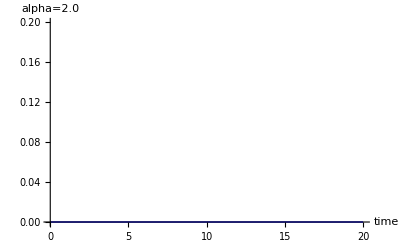

```mathematica
"Impulse Solutions"
a=2.0;
x0=0;
Xin=UnitStep[t];
Y=Sqrt[a/π]Exp[-a*t^2];
diffsol=NDSolve[{x1'[t]==Y-(1+a)*x1[t]+a*x2[t],
x2'[t]==x1[t]-(1+a)*x2[t]+a*x3[t],
x3'[t]==x2[t]-(1+a)*x3[t]+a*x4[t],
x4'[t]==x3[t]-(1+a)*x4[t]+a*x5[t],
x5'[t]==x4[t]-(1+a)*x5[t]+a*x6[t],
x6'[t]==x5[t]-(1+a)*x6[t]+a*x7[t],
x7'[t]==x6[t]-(1+a)*x7[t]+a*x8[t],
x8'[t]==x7[t]-(1+a)*x8[t]+a*x9[t],
x9'[t]==x8[t]-(1+a)*x9[t]+a*x10[t],
x10'[t]==x9[t]-(1+a)*x10[t]+a*x11[t],
x11'[t]==x10[t]-(1+a)*x11[t]+a*x12[t],
x12'[t]==x11[t]-(1+a)*x12[t]+a*x13[t],
x13'[t]==x12[t]-(1+a)*x13[t]+a*x14[t],
x14'[t]==x13[t]-(1+a)*x14[t]+a*x15[t],
x15'[t]==x14[t]-(1+a)*x15[t]+a*x16[t],
x16'[t]==x15[t]-(1+a)*x16[t]+a*x17[t],
x17'[t]==x16[t]-(1+a)*x17[t]+a*x18[t],
x18'[t]==x17[t]-(1+a)*x18[t]+a*x19[t],
x19'[t]==x18[t]-(1+a)*x19[t]+a*x20[t],
x20'[t]==x19[t]-(1+a)*x20[t],x1[0]==0,x2[0]==0,x3[0]==0,x4[0]==0,x5[0]==0,x6[0]==0,x7[0]==0,x8[0]==0,x9[0]==0,x10[0]==0,x11[0]==0,x12[0]==0,x13[0]==0,x14[0]==0,x15[0]==0,x16[0]==0,x17[0]==0,x18[0]==0,x19[0]==0,x20[0]==0},{x1[t],x2[t],x3[t],x4[t],x5[t],x6[t],x7[t],x8[t],x9[t],x10[t],x11[t],x12[t],x13[t],x14[t],x15[t],x16[t],x17[t],x18[t],x19[t],x20[t]},{t,0,200}];

{x1out[t_],x2out[t_],x3out[t_],x4out[t_],x5out[t_],x6out[t_],x7out[t_],x8out[t_],x9out[t_],x10out[t_],x11out[t_],x12out[t_],x13out[t_],x14out[t_],x15out[t_],x16out[t_],x17out[t_],x18out[t_],x19out[t_],x20out[t_]}={x1[t],x2[t],x3[t],x4[t],x5[t],x6[t],x7[t],x8[t],x9[t],x10[t],x11[t],x12[t],x13[t],x14[t],x15[t],x16[t],x17[t],x18[t],x19[t],x20[t]}/.Flatten[diffsol];
Plot[x20out[t],{t,0,20},AxesLabel->{"time","alpha=2.0","Response to Unit Step Perturbation"},PlotStyle->{RGBColor[0,0,1]},PlotRange->{0,.20}]
```

```mathematica
"Part III:Perturbations in the Liquid and Vapor Inlet concentrations"
```